```mathematica
eta[r_,R_,DR_,etac_,etashi_,etasho_,etasol_]:=Module[{m=(etasho-etashi)/DR,b=-(etasho-etashi)/DR*R+etashi},Piecewise[{{etac,Abs[r]<R},{m*Abs[r]+b,Abs[r]≥R && Abs[r]≤R+DR},{etasol,Abs[r]>R+DR}}]]
```

```mathematica
eta[r,1,0.5,1,1,0.5,0]
```

Piecewise[{{1, Abs[r]<1}, {2.-1. Abs[r], Abs[r]≥1&&Abs[r]≤1.5}, {0, True}}]

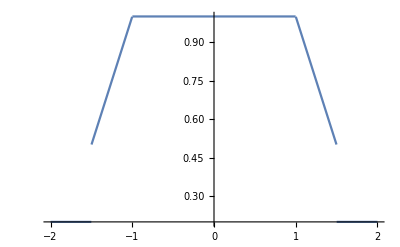

```mathematica
Plot[eta[r,1,0.5,1,1,0.5,0.2],{r,-2,2}]
```

```mathematica
Integrate[BesselJ[0,Q*r]*2*Pi*r*eta[r,R,DR,etac-etasolv,etashi-etasolv,etasho-etasolv,etasolv-etasolv],{r,0,R},Assumptions->R>0&&DR>0,Assumptions->R>0&&DR>0&&Q>0]
```

(2 (etac-etasolv) π R BesselJ[1,Q R])/Q

```mathematica
FullSimplify[Integrate[BesselJ[0,Q*r]*2*Pi*r*eta[r,R,DR,etac-etasolv,etashi-etasolv,etasho-etasolv,etasolv-etasolv],{r,R,R+DR},Assumptions->R>0&&DR>0&&Q>0]]
```

(π ((6 (DR (etashi-etasolv)+(etashi-etasho) R) (-R BesselJ[1,Q R]+(DR+R) BesselJ[1,Q (DR+R)]))/Q+2 (etashi-etasho) (R^3 HypergeometricPFQ[{3/2},{1,5/2},-1/4 Q^2 R^2]-(DR+R)^3 HypergeometricPFQ[{3/2},{1,5/2},-1/4 Q^2 (DR+R)^2])))/(3 DR)

```mathematica
Integrate[BesselJ[0,Q*r]*2*Pi*r*eta[r,R,DR,etac-etasolv,etashi-etasolv,etasho-etasolv,etasolv-etasolv],{r,R+DR,Infinity},Assumptions->R>0&&DR>0&&Q>0]
```

0

```mathematica
FullSimplify[Integrate[BesselJ[0,Q*r]*2*Pi*r*eta[r,R,DR,etac-etasolv,etashi-etasolv,etasho-etasolv,etasolv-etasolv],{r,0,Infinity},Assumptions->R>0&&DR>0&&Q>0]]
```

1/(DR Q^2)π (2 DR Q ((etac-etashi) R BesselJ[1,Q R]+(etasho-etasolv) (DR+R) BesselJ[1,Q (DR+R)])+(etashi-etasho) π (-R BesselJ[1,Q R] StruveH[0,Q R]+(DR+R) BesselJ[1,Q (DR+R)] StruveH[0,Q (DR+R)]+R BesselJ[0,Q R] StruveH[1,Q R]-(DR+R) BesselJ[0,Q (DR+R)] StruveH[1,Q (DR+R)]))

```mathematica
CForm[1/(DR Q^2)π (2 DR Q ((etac-etashi) R BesselJ[1,Q R]+(etasho-etasolv) (DR+R) BesselJ[1,Q (DR+R)])+(etashi-etasho) π (-R BesselJ[1,Q R] StruveH[0,Q R]+(DR+R) BesselJ[1,Q (DR+R)] StruveH[0,Q (DR+R)]+R BesselJ[0,Q R] StruveH[1,Q R]-(DR+R) BesselJ[0,Q (DR+R)] StruveH[1,Q (DR+R)]))]
```

(Pi*(2*DR*Q*((etac - etashi)*R*BesselJ(1,Q*R) + (etasho - etasolv)*(DR + R)*BesselJ(1,Q*(DR + R))) + 
       (etashi - etasho)*Pi*(-(R*BesselJ(1,Q*R)*StruveH(0,Q*R)) + (DR + R)*BesselJ(1,Q*(DR + R))*StruveH(0,Q*(DR + R)) + R*BesselJ(0,Q*R)*StruveH(1,Q*R) - (DR + R)*BesselJ(0,Q*(DR + R))*StruveH(1,Q*(DR + R)))))/
   (DR*Power(Q,2))

```mathematica
CForm[FullSimplify[Limit[1/(DR Q^2)π (2 DR Q ((etac-etashi) R BesselJ[1,Q R]+(etasho-etasolv) (DR+R) BesselJ[1,Q (DR+R)])+(etashi-etasho) π (-R BesselJ[1,Q R] StruveH[0,Q R]+(DR+R) BesselJ[1,Q (DR+R)] StruveH[0,Q (DR+R)]+R BesselJ[0,Q R] StruveH[1,Q R]-(DR+R) BesselJ[0,Q (DR+R)] StruveH[1,Q (DR+R)])),Q->0]]]
```

(Power(DR,2)*(etashi + 2*etasho - 3*etasolv)*Pi)/3. + DR*(etashi + etasho - 2*etasolv)*Pi*R + (etac - etasolv)*Pi*Power(R,2)

```mathematica
FullSimplify[Integrate[2 Pi r*(1-(r/R)^2)^(alpha/2-2),{r,0,R},Assumptions->R>0&&alpha>2]]
```

(2 π R^2)/(-2+alpha)

```mathematica
Integrate[2 Pi*BesselJ[0,q*r]*r *(1-(r/R)^2)^(alpha/2-2),{r,0,R},Assumptions->R>0&&alpha>2&&q>0]
```

(2 π R^2 Hypergeometric0F1[alpha/2,-1/4 q^2 R^2])/(-2+alpha)

```mathematica
Series[(2 π R^2 Hypergeometric0F1[alpha/2,-1/4 q^2 R^2])/(-2+alpha),{q,Infinity,0}]
```

q^(-alpha/2) (Cos[π/4-(alpha π)/4+q √(R^2)] ((2^(1/2+alpha/2) √π (R^2)^(5/4-alpha/4) Gamma[alpha/2] √q)/(-2+alpha)+O[1/q]^(3/2))+(-(2^(-5/2+alpha/2) (-3+alpha) (-1+alpha) √π (R^2)^(3/4-alpha/4) Gamma[alpha/2] √(1/q))/(-2+alpha)+O[1/q]^(3/2)) Sin[π/4-(alpha π)/4+q √(R^2)])

```mathematica
Integrate[4 Pi*Sin[q*r]/(q*r)*r^2 *(1-(r/R)^2)^(alpha/2-2),{r,0,R},Assumptions->R>0&&alpha>2&&q>0]
```

π^(3/2) R^3 Gamma[-1+alpha/2] Hypergeometric0F1Regularized[(1+alpha)/2,-1/4 q^2 R^2]

```mathematica
Integrate[4Pi*r^2 *(1-(r/R)^2)^(alpha/2-2),{r,0,R},Assumptions->R>0&&alpha>2&&q>0]
```

(π^(3/2) R^3 Gamma[-1+alpha/2])/Gamma[(1+alpha)/2]

```mathematica
Integrate[R^2*BesselJ[1,q*R]/(q*R)*Exp[-q^2*sigma^2/2]*BesselJ[0,q*r]*q,{q,0,Infinity},Assumptions->R>0&&r≥0]
```

Integrate[ⅇ^(-1/2 q^2 sigma^2) R BesselJ[0,q r] BesselJ[1,q R],{q,0,∞},Assumptions→R>0&&r≥0]

```mathematica
Normal[Series[R^2*BesselJ[1,q*R]/(q*R)*Exp[-q^2*sigma^2/2]*BesselJ[0,q*r]*q,{r,R-sigma,4}]]
```

ⅇ^(-1/2 q^2 sigma^2) R BesselJ[0,q R-q sigma] BesselJ[1,q R]-ⅇ^(-1/2 q^2 sigma^2) q R (r-R+sigma) BesselJ[1,q R] BesselJ[1,q R-q sigma]+(ⅇ^(-1/2 q^2 sigma^2) q R (r-R+sigma)^4 (-3+q^2 R^2-2 q^2 R sigma+q^2 sigma^2) BesselJ[1,q R] (-q R BesselJ[0,q R-q sigma]+q sigma BesselJ[0,q R-q sigma]+2 BesselJ[1,q R-q sigma]))/(24 (-R+sigma)^3)+1/(6 (-R+sigma)^2)ⅇ^(-1/2 q^2 sigma^2) q R (r-R+sigma)^3 BesselJ[1,q R] (q R BesselJ[0,q R-q sigma]-q sigma BesselJ[0,q R-q sigma]-2 BesselJ[1,q R-q sigma]+q^2 R^2 BesselJ[1,q R-q sigma]-2 q^2 R sigma BesselJ[1,q R-q sigma]+q^2 sigma^2 BesselJ[1,q R-q sigma])+ⅇ^(-1/2 q^2 sigma^2) q^2 R (r-R+sigma)^2 BesselJ[1,q R] (-1/2 BesselJ[0,q R-q sigma]+BesselJ[1,q R-q sigma]/(2 (q R-q sigma)))

```mathematica
FullSimplify[Integrate[ⅇ^(-1/2 q^2 sigma^2) R BesselJ[0,q R-q sigma] BesselJ[1,q R]-ⅇ^(-1/2 q^2 sigma^2) q R (r-R+sigma) BesselJ[1,q R] BesselJ[1,q R-q sigma]+(ⅇ^(-1/2 q^2 sigma^2) q R (r-R+sigma)^4 (-3+q^2 R^2-2 q^2 R sigma+q^2 sigma^2) BesselJ[1,q R] (-q R BesselJ[0,q R-q sigma]+q sigma BesselJ[0,q R-q sigma]+2 BesselJ[1,q R-q sigma]))/(24 (-R+sigma)^3)+1/(6 (-R+sigma)^2)ⅇ^(-1/2 q^2 sigma^2) q R (r-R+sigma)^3 BesselJ[1,q R] (q R BesselJ[0,q R-q sigma]-q sigma BesselJ[0,q R-q sigma]-2 BesselJ[1,q R-q sigma]+q^2 R^2 BesselJ[1,q R-q sigma]-2 q^2 R sigma BesselJ[1,q R-q sigma]+q^2 sigma^2 BesselJ[1,q R-q sigma])+ⅇ^(-1/2 q^2 sigma^2) q^2 R (r-R+sigma)^2 BesselJ[1,q R] (-1/2 BesselJ[0,q R-q sigma]+BesselJ[1,q R-q sigma]/(2 (q R-q sigma))),{q,0,Infinity},Assumptions->R>0&&r≥0&&sigma>0]]
```

Integrate[1/(24 (R-sigma)^2)ⅇ^(-1/2 q^2 sigma^2) R BesselJ[1,q R] (4 (R-sigma) (6 (R-sigma)+q^2 (r-R+sigma)^2 (r-4 R+4 sigma)) BesselJ[0,q (R-sigma)]+q (r-R+sigma) (4 (r^2 (-2+q^2 (R-sigma)^2)-r (-7+2 q^2 (R-sigma)^2) (R-sigma)+(-11+q^2 (R-sigma)^2) (R-sigma)^2) BesselJ[1,q (R-sigma)]-q (-3+q^2 (R-sigma)^2) (r-R+sigma)^3 BesselJ[2,q (R-sigma)])),{q,0,∞},Assumptions→R>0&&r≥0&&sigma>0]

```mathematica
Integrate[Exp[-1/2*((x)^2+y^2)/sigma^2],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

ConditionalExpression[2 π sigma^2,Re[sigma^2]>0]

```mathematica
Integrate[Exp[-1/2*((x-r)^2+y^2)/sigma^2],{x,0,R},{y,-Infinity,Infinity}]
```

(π sigma (Erf[r/(√2 sigma)]-Erf[(r-R)/(√2 sigma)]))/(√(1/sigma^2))

```mathematica
eta[r_,R_,sigma_]:=1/24 (12+1/sigma^8 ⅇ^(-R^2/sigma^2) (-(4 (-1+r)^4 R^8-8 (-1+r)^3 R^6 sigma^2+(-1+r)^2 (19+r (-10+3 r)) R^4 sigma^4+12 sigma^8) BesselI[0,R^2/sigma^2]+(-1+r) R^2 (4 (-1+r)^3 R^6+2 (-5+r) (-1+r)^2 R^4 sigma^2+(-1+r) (19+r (-10+3 r)) R^2 sigma^4+2 (-25+r (23+r (-13+3 r))) sigma^6) BesselI[1,R^2/sigma^2]))
```

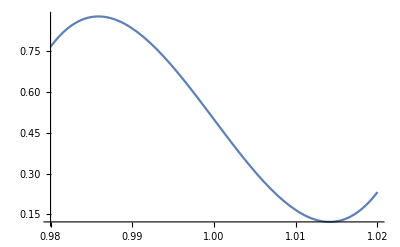

```mathematica
Plot[eta[r,1,0.01],{r,0.98,1.02},PlotRange->All]
```

```mathematica
eta2[r_,R_,sigma_]:=1/2 (Erf[r/(√2 sigma)]-Erf[(r-R)/(√2 sigma)])
```

```mathematica
FullSimplify[eta2[r,R,sigma],Assumptions->sigma>0]
```

1/2 (Erf[r/(√2 sigma)]-Erf[(r-R)/(√2 sigma)])

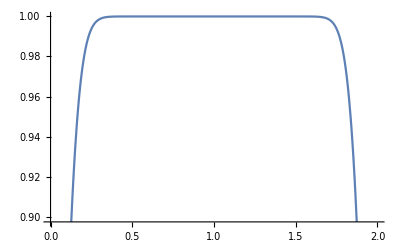

```mathematica
Plot[eta2[r,2,0.1],{r,0,2}]
```